```mathematica
Exit[]
```

```mathematica
PacletDirectoryLoad["/Users/daniels/Library/CloudStorage/OneDrive-Personal/projects/thesis/wolfram-vm/PatternMatcher"];
```

```mathematica
Needs["DanielS`PatternMatcher`"]
```

```mathematica
f[x]
```

f[x]

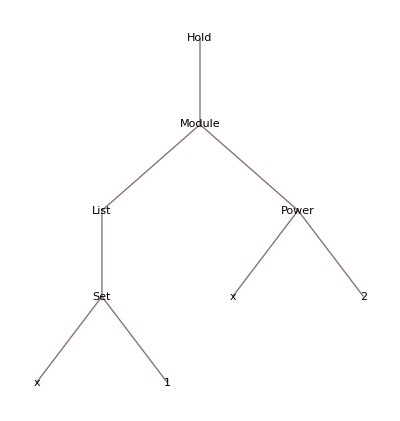

```mathematica
Hold[Module[{x=1},x^2]]//TreeForm
```

```mathematica
expr=f[x_Integer];
```

```mathematica
CompilePatternToBytecode[expr]
```

PatternBytecode[…]

```mathematica
MatchQ[5,_Integer]
```

True

```mathematica
MatchQ[5.4,x_Integer/;OddQ[x]]
```

False

```mathematica
f[x_Integer]:=x+1
f[x_Real]:=x*x
```

```mathematica
DownValues[f]
```

{HoldPattern[f[x_Integer]]:>x+1,HoldPattern[f[x_Real]]:>x x}

```mathematica
MatchQ[f,f]
```

```mathematica
PatternBytecodeDisassemble[f[_]]
```

L0:
 0    BEGIN_BLOCK     Label[0]
L3:
 1      BEGIN_BLOCK     Label[3]
 2        MATCH_LENGTH    %e0, 1, Label[4]
 3        MATCH_HEAD      %e0, Expr[f], Label[4]
 4        MOVE            %e1, %e0
 5        GET_PART        %e2, %e0, 1
 6        MOVE            %e0, %e2
 7        MOVE            %e0, %e1
 8      END_BLOCK       Label[3]
 9      JUMP            Label[2]  → L2
L4:
10      JUMP            Label[1]  → L1
L5:
11    END_BLOCK       Label[0]
L1:
12    LOAD_IMM        %b0, 0
13    HALT            
L2:
14    EXPORT_BINDINGS 
15    LOAD_IMM        %b0, 1
16    HALT            

========================================
Statistics:
  Instructions:      17
  Labels:            6
  Expr registers:    3
  Bool registers:    1
  Blocks:            2 (max depth: 2)
  Jumps:             2
  Backtrack points:  0

```mathematica
PatternBytecodeDisassemble[f[x_Integer]]
```

L0:
 0    BEGIN_BLOCK     Label[0]
L3:
 1      BEGIN_BLOCK     Label[3]
 2        MATCH_LENGTH    %e0, 1, Label[4]
 3        MATCH_HEAD      %e0, Expr[f], Label[4]
 4        MOVE            %e1, %e0
 5        GET_PART        %e2, %e0, 1
 6        MOVE            %e0, %e2
 7        MATCH_HEAD      %e0, Expr[Integer], Label[5]
 8        MOVE            %e3, %e0
 9        BIND_VAR        Symbol["Global`x"], %e3
10        JUMP            Label[6]  → L6
L5:
11        JUMP            Label[4]  → L4
L6:
12        MOVE            %e0, %e1
13      END_BLOCK       Label[3]
14      JUMP            Label[2]  → L2
L4:
15      JUMP            Label[1]  → L1
L7:
16    END_BLOCK       Label[0]
L1:
17    LOAD_IMM        %b0, 0
18    HALT            
L2:
19    EXPORT_BINDINGS 
20    LOAD_IMM        %b0, 1
21    HALT            

========================================
\!\(\*StyleBox["Statistics:", FontWeight -> Bold, FontColor -> RGBColor[0.2, 0.2, 0.5]]\)
  Instructions:      22
  Labels:            8
  Expr registers:    4
  Bool registers:    1
  Blocks:            2 (max depth: 2)
  Jumps:             4
  Backtrack points:  0

\!\(\*StyleBox["Lexical bindings:", FontWeight -> Bold, FontColor -> RGBColor[0.2, 0.2, 0.5]]\)
  Global`x     \!\(\*StyleBox["→", FontColor -> RGBColor[0.5, 0.5, 0.5]]\) \!\(\*StyleBox["%e3", FontWeight -> Bold, FontColor -> RGBColor[0.2, 0.6, 0.3]]\)

-Graphics-

```mathematica
Exit[]
```

```mathematica
PatternMatcherEnableTrace[True];
PatternMatcherExecute[f[x_Integer],f[5]]
```

⋮ BEGIN_BLOCK L0 depth = 1

⋮ BEGIN_BLOCK L3 depth = 2

☑ MATCH_LENGTH SUCCESS  %e0 len = 1 expected = 1

☑ MATCH_HEAD SUCCESS  %e0 == f

• MOVE %e 1[LongLeftArrow]%e 0 = f[5]

» GET_PART %e2 := part(%e 0,1)

• MOVE %e 0[LongLeftArrow]%e 2 = 5

☑ MATCH_HEAD SUCCESS  %e0 == Integer

• MOVE %e 3[LongLeftArrow]%e 0 = 5

↧ BIND_VAR Global`x[LongLeftArrow]%e 3 = 5 (no trail)

→ JUMP L6 pc = 12

• MOVE %e 0[LongLeftArrow]%e 1 = f[5]

• SAVE_BINDINGS 1 bindings copied

⋮ END_BLOCK L3 depth = 1 (merged)

→ JUMP L2 pc = 19

• SAVE_BINDINGS 1 bindings copied

• EXPORT_BINDINGS saved 1bindings

• LOAD_IMM %b 0[LongLeftArrow]True

• HALT stopping executioncycles = 17

<|Result→True,CyclesExecuted→17,Bindings→<|Global`x→5|>|>

```mathematica
PatternMatcherEnableTrace[True]
```

True

```mathematica
MatchQ[g[4],g[_]]
```

True

```mathematica
MatchQ[h[4],g[_]]
```

False

```mathematica
PatternBytecodeDisassemble[g[_]]
```

L0:
 0    BEGIN_BLOCK     Label[0]
L3:
 1      BEGIN_BLOCK     Label[3]
 2        MATCH_LENGTH    %e0, 1, Label[4]
 3        MATCH_HEAD      %e0, Expr[g], Label[4]
 4        MOVE            %e1, %e0
 5        GET_PART        %e2, %e0, 1
 6        MOVE            %e0, %e2
 7        MOVE            %e0, %e1
 8      END_BLOCK       Label[3]
 9      JUMP            Label[2]  → L2
L4:
10      JUMP            Label[1]  → L1
L5:
11    END_BLOCK       Label[0]
L1:
12    LOAD_IMM        %b0, 0
13    HALT            
L2:
14    EXPORT_BINDINGS 
15    LOAD_IMM        %b0, 1
16    HALT            

========================================
Statistics:
  Instructions:      17
  Labels:            6
  Expr registers:    3
  Bool registers:    1
  Blocks:            2 (max depth: 2)
  Jumps:             2
  Backtrack points:  0

```mathematica
PatternMatcherExecute[g[_],g[5]]
```

⋮ BEGIN_BLOCK L0 depth = 1

⋮ BEGIN_BLOCK L3 depth = 2

☑ MATCH_LENGTH SUCCESS  %e0 len = 1 expected = 1

☑ MATCH_HEAD SUCCESS  %e0 == g

• MOVE %e 1\[LongLeftArrow]%e 0 = g[5]

» GET_PART %e2 := part(%e 0,1)

• MOVE %e 0\[LongLeftArrow]%e 2 = 5

• MOVE %e 0\[LongLeftArrow]%e 1 = g[5]

• SAVE_BINDINGS 0 bindings copied

⋮ END_BLOCK L3 depth = 1 (merged)

→ JUMP L2 pc = 14

• SAVE_BINDINGS 0 bindings copied

• EXPORT_BINDINGS saved 0bindings

• LOAD_IMM %b 0\[LongLeftArrow]True

• HALT stopping executioncycles = 13

<|Result→True,CyclesExecuted→13,Bindings→<||>|>

```mathematica
"• ""MOVE"""" ""%e 0 \\[LongLeftArrow] %e 2 = 5"
```

• MOVE %e 0 \[LongLeftArrow] %e 2 = 5

```mathematica
"⟵"//ToCharacterCode
```

{10229}